# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model

## A Quantum-Like Approach

### Normal form approach

We propose we can understand IIG as the sequence of two normal-form game - demands and crisis games
In each of these two game, both actors have a strategic set of two strategies, from which they choose simultaneously

demands game | D2 | nD2
D1 | crisis game | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

 crisis game  | F2 | nF2
F1 | U1War, U2War | U1Cap2, U2Cap2
nF1 | U1Cap1, U2Cap1 | U1Nego, U2Nego
(we need to deal with the fact that we do not distinguish utilities of War1 and War2 in normal form game - we currently use an average of the two)

we take Signorino formula for the conditional probability of choosing between the strategies given their utilities and the expected strategy of the other player
p(F1|F2) = exp(lambda*U1War)/(exp(lambda*U1War)+exp(lambda*U1Cap1))

which results in following probability amplitudes

```mathematica
(* for debugging *)
(* U1SQ=-0.23801; U1Acq2=1.025024; U1Acq1=-1.36844;U1Nego=-1.10122; U1Cap1=-2.25679; U1Cap2=1.051597;U1War1=-1.51882; U1War2=-1.963;
U2SQ = -0.57593; U2Acq2 = -1.51157; U2Acq1=0.627684;U2Nego=0.591662; U2Cap1=0.861688; U2Cap2=-1.52841;U2War1 = 0.808828; U2War2=0.817247;
λ = 1; *)
```

```mathematica
(* U1War = Mean[{U1War1,U1War2}]; 
U2War = Mean[{U2War1,U2War2}]; *)
```

```mathematica
(* =====CRISIS GAME AMPLITUDE FUNCTIONS=====*)
(*Player 1's amplitude for fighting after Player 2 fights*)
```

```mathematica
aF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1War);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 fights*)
aNF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap1);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for fighting after Player 2 doesn't fight*)
aF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap2);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 doesn't fight*)
aNF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Nego);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 fights*)
aF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2War);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 fights*)
aNF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap2);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 doesn't fight*)
aF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap1);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 doesn't fight*)
aNF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Nego);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];
```

#### Crisis Game Probability Functions

```mathematica
(*Combined amplitude for Player 1 fighting*)
aF1[pF2norm_,aF1afterF2_,aF1afterNF2_]:=(Sqrt[pF2norm]*aF1afterF2)+(Sqrt[1-pF2norm]*aF1afterNF2);

(*Probability of Player 1 fighting*)
pF1[aF1_]:=aF1*Conjugate[aF1];

(*Combined amplitude for Player 1 not fighting*)
aNF1[pF2norm_,aNF1afterF2_,aNF1afterNF2_]:=(Sqrt[pF2norm]*aNF1afterF2)+(Sqrt[1-pF2norm]*aNF1afterNF2);

(*Probability of Player 1 not fighting*)
pNF1[aNF1_]:=aNF1*Conjugate[aNF1];

(*Normalized probability of Player 1 fighting*)
pF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pF1/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 1 not fighting*)
pNF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pNF1/denominator] (*Avoid division by zero*)];

(*Combined amplitude for Player 2 fighting*)
aF2[pF1norm_,aF2afterF1_,aF2afterNF1_]:=(Sqrt[pF1norm]*aF2afterF1)+(Sqrt[1-pF1norm]*aF2afterNF1);

(*Probability of Player 2 fighting*)
pF2[aF2_]:=aF2*Conjugate[aF2];

(*Combined amplitude for Player 2 not fighting*)
aNF2[pF1norm_,aNF2afterF1_,aNF2afterNF1_]:=(Sqrt[pF1norm]*aNF2afterF1)+(Sqrt[1-pF1norm]*aNF2afterNF1);

(*Probability of Player 2 not fighting*)
pNF2[aNF2_]:=aNF2*Conjugate[aNF2];

(*Normalized probability of Player 2 fighting*)
pF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pF2/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 2 not fighting*)
pNF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pNF2/denominator] (*Avoid division by zero*)];
```

pF1 = pF2 * pF1afterF2 + pNF2 * pF1afterNF2 + 2*Sqrt[pF2*pNF2]*aF1afterF2*aF1afterNF2*Cos[θ1a-θ1b]
pF1 depends only phase difference Δθ1 = θ1a-θ1b, as expected

that gives us two equations with two variables (pF1norm, pF2norm) => unique set of pF1norm, pF2norm satisfying the conditions
in our balanced dataset, we have 375 cases (War1, War2, Cap1, Cap2, Nego) of crisis game, we can look at this stage of IIG, without combining it with demands game
we can look for what combination of Δθ1 and Δθ2 does the model has the highest fit with the empirical observations

#### Demands Game

to add the demand stage of the game (needed for the comparability to Signorino and de Mesquita), we proceed analogically to crisis game

demands game | D2 | nD2
D1 | U1Cris, U2Cris | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

```mathematica
U1Cris := (pF1norm*pF2norm*U1War)+(pF1norm*(1-pF2norm)*U1Cap2)+((1-pF1norm)*pF2norm*U1Cap1)+((1-pF1norm)*(1-pF2norm)*U1Nego);
U2Cris := (pF1norm*pF2norm*U2War)+(pF1norm*(1-pF2norm)*U2Cap2)+((1-pF1norm)*pF2norm*U2Cap1)+((1-pF1norm)*(1-pF2norm)*U2Nego);
```

```mathematica
(*Player 1's amplitude for demanding after Player 2 demands*)
aD1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cris);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 demands*)
aND1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq1);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for demanding after Player 2 doesn't demand*)
aD1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq2);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 doesn't demand*)
aND1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1SQ);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 demands*)
aD2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cris);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 demands*)
aND2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq2);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 doesn't demand*)
aD2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq1);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 doesn't demand*)
aND2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2SQ);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];
```

```mathematica
(* =====DEMANDS GAME PROBABILITY FUNCTIONS=====*)
```

```mathematica
(*Combined amplitude for Player 1 demanding*)
aD1[pD2norm_,aD1afterD2_,aD1afterND2_]:=(Sqrt[pD2norm]*aD1afterD2)+(Sqrt[1-pD2norm]*aD1afterND2);

(*Probability of Player 1 demanding*)
pD1[aD1_]:=aD1*Conjugate[aD1];

(*Combined amplitude for Player 1 not demanding*)
aND1[pD2norm_,aND1afterD2_,aND1afterND2_]:=(Sqrt[pD2norm]*aND1afterD2)+(Sqrt[1-pD2norm]*aND1afterND2);

(*Probability of Player 1 not demanding*)
pND1[aND1_]:=aND1*Conjugate[aND1];

(*Normalized probability of Player 1 demanding*)
pD1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pD1/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 1 not demanding*)
pND1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pND1/denominator] (*Avoid division by zero*)];

(*Combined amplitude for Player 2 demanding*)
aD2[pD1norm_,aD2afterD1_,aD2afterND1_]:=(Sqrt[pD1norm]*aD2afterD1)+(Sqrt[1-pD1norm]*aD2afterND1);

(*Probability of Player 2 demanding*)
pD2[aD2_]:=aD2*Conjugate[aD2];

(*Combined amplitude for Player 2 not demanding*)
aND2[pD1norm_,aND2afterD1_,aND2afterND1_]:=(Sqrt[pD1norm]*aND2afterD1)+(Sqrt[1-pD1norm]*aND2afterND1);

(*Probability of Player 2 not demanding*)
pND2[aND2_]:=aND2*Conjugate[aND2];

(*Normalized probability of Player 2 demanding*)
pD2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pD2/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 2 not demanding*)
pND2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pND2/denominator] (*Avoid division by zero*)];
```

now there are 4 phases which we can to solve for to find the best fit with the empirical observations
Δθ1 ... phase connected to the decision to “fight/not fight” of the 1st player
Δθ2 ... phase connected to the decision to “fight/not fight” of the 2nd player
Δθ3 ... phase connected to the decision to “demand/not demand” of the 1st player
Δθ4 ... phase connected to the decision to “demand/not demand” of the 2nd player

we can set Δθ1=Δθ3 and Δθ2=Δθ4 if necessary

## Functions

### FindCrisisEquilibrium

```mathematica
(*
FindCrisisEquilibrium:
  Finds the equilibrium probabilities for the crisis game given utility values and phase differences between quantum states.
Parameters:
	 -u1War,u1Cap1,u1Cap2,u1Nego:Player 1's utilities for different outcomes
	-u2War,u2Cap2,u2Cap1,u2Nego:Player 2's utilities for different outcomes
	-lambda:Decision parameter controlling rationality (higher=more rational)
	-deltaTheta1,deltaTheta2:Phase differences for Players 1 and 2
	-maxIter:Maximum number of iterations for convergence
	-tolerance:Convergence threshold
  -verbose:Whether to record detailed iteration history
*)

FindCrisisEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u2War_,
				      u2Cap2_,u2Cap1_,u2Nego_,
				      lambda_,deltaTheta1_,deltaTheta2_,
				      maxIter_:100,tolerance_:10^-6,
				      verbose_:False]:=
Module[{
pF1normCurrent=0.5,
pF2normCurrent=0.5,
pF1normNext,
pF2normNext,
a1F2,a1NF2,a1F1,a1NF1,p1F1,p1NF1,
a2F1,a2NF1,a2F2,a2NF2,p2F2,p2NF2,
theta1a,theta1b,theta2a,theta2b,
pWar,pCap2,pCap1,pNego,
iter=0,converged=False,
iterationHistory={},
totalProb},

(*Set phase differences*)
theta1a=deltaTheta1/2;
theta1b=-deltaTheta1/2;
theta2a=deltaTheta2/2;
theta2b=-deltaTheta2/2;

(*Initial probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Keep a log for debugging purposes*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->0,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"pWar"->Re[pWar],
"pCap2"->Re[pCap2],
"pCap1"->Re[pCap1],
"pNego"->Re[pNego],
"TotalProb"->pWar+pCap2+pCap1+pNego
|>
]
];

While[iter<maxIter&&!converged,

(*Calculate amplitudes for player 1*)
a1F2=aF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1NF2=aNF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1F1=aF1[pF2normCurrent,a1F2,aF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
a1NF1=aNF1[pF2normCurrent,a1NF2,aNF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
p1F1=pF1[a1F1];
p1NF1=pNF1[a1NF1];
pF1normNext=pF1norm[p1F1,p1NF1];

(*Calculate amplitudes for player 2*)
a2F1=aF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2NF1=aNF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2F2=aF2[pF1normCurrent,a2F1,aF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
a2NF2=aNF2[pF1normCurrent,a2NF1,aNF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
p2F2=pF2[a2F2];
p2NF2=pNF2[a2NF2];
pF2normNext=pF2norm[p2F2,p2NF2];

(*Calculate outcome probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Check total probability for consistency*)
totalProb=pWar+pCap2+pCap1+pNego;
If[Abs[totalProb-1.0]>10^-10,
Print["Warning: Total probability differs from 1.0: ",totalProb];
];

(*Calculate convergence before updating values*)
converged=
Abs[pF1normNext-pF1normCurrent]<tolerance&&
Abs[pF2normNext-pF2normCurrent]<tolerance;

(*Track iteration if verbose*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->iter,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"DeltapF1"->Abs[pF1normNext-pF1normCurrent],
"DeltapF2"->Abs[pF2normNext-pF2normCurrent],
"pWar"->pWar,
"pCap2"->pCap2,
"pCap1"->pCap1,
"pNego"->pNego,
"TotalProb"->totalProb|>
]
];

(*Update for next iteration*)
pF1normCurrent=Re[pF1normNext];
pF2normCurrent=Re[pF2normNext];
iter++;];

(*Return equilibrium probabilities and outcomes*)
<|
"Converged"->converged,
"Iterations"->iter,
"pF1"->Re[pF1normCurrent],
	"pF2"->Re[pF2normCurrent],
	"pWar"->pWar,
	"pCap2"->pCap2,
	"pCap1"->pCap1,
	"pNego"->pNego,
	"TotalProb"->totalProb,
	"IterationHistory"->If[verbose,iterationHistory,Null]
|>
];
```

### FindFullEquilibrium

```mathematica
(*
   FindFullEquilibrium:Finds the equilibrium for the full game (demands+crisis) given utility values and phase differences.
Parameters:
	 -u1War,u1Cap1,u1Cap2,u1Nego,u1SQ,u1Acq1,u1Acq2:Player 1's utilities
	-u2War,u2Cap2,u2Cap1,u2Nego,u2SQ,u2Acq1,u2Acq2:Player 2's utilities
	-lambda:Decision parameter
	-deltaTheta1,deltaTheta2:Phase differences for crisis game
	-deltaTheta3,deltaTheta4:Phase differences for demands game
	-maxIter:Maximum iterations
	-tolerance:Convergence threshold
  -verbose:Detailed logging
*)
FindFullEquilibrium[
u1War_,u1Cap1_,u1Cap2_,u1Nego_,u1SQ_,
u1Acq1_,u1Acq2_,u2War_,u2Cap2_,u2Cap1_,
u2Nego_,u2SQ_,u2Acq1_,u2Acq2_,
lambda_,
deltaTheta1_,deltaTheta2_,deltaTheta3_,deltaTheta4_,
maxIter_:100,
tolerance_:10^-6,
verbose_:False
]:=
	Module[{
	crisisEq,u1Cris,u2Cris,
	pD1normCurrent=0.5,pD2normCurrent=0.5,
	pD1normNext,pD2normNext,
	a1D2,a1ND2,a1D1,a1ND1,p1D1,p1ND1,
	a2D1,a2ND1,a2D2,a2ND2,p2D2,p2ND2,
	crisisPWar,crisisPCap1,crisisPCap2,crisisPNego,
	theta3a,theta3b,theta4a,theta4b,
	pCrisis,pAcq2,pAcq1,pSQ,totalProb,
	iter=0,converged=False,iterationHistory={}
},

(*Set phase differences for demands game*)
theta3a=deltaTheta3/2;
theta3b=-deltaTheta3/2;
theta4a=deltaTheta4/2;
theta4b=-deltaTheta4/2;

(*First find crisis game equilibrium*)
crisisEq=FindCrisisEquilibrium[
			u1War,u1Cap1,u1Cap2,u1Nego,u2War,u2Cap2,u2Cap1,u2Nego,
			lambda,deltaTheta1,deltaTheta2,maxIter,tolerance,verbose
];

(*Check if crisis game converged*)
If[!crisisEq["Converged"],
If[verbose,Print["Warning: Crisis game did not converge."]];
];

(*Extract the individual probability values*)
crisisPWar=crisisEq["pWar"];
crisisPCap1=crisisEq["pCap1"];
crisisPCap2=crisisEq["pCap2"];
crisisPNego=crisisEq["pNego"];

(*Calculate expected crisis utilities*)
u1Cris=crisisPWar*u1War+crisisPCap2*u1Cap2+crisisPCap1*u1Cap1+crisisPNego*u1Nego;
u2Cris=crisisPWar*u2War+crisisPCap2*u2Cap2+crisisPCap1*u2Cap1+crisisPNego*u2Nego;

(*Handle extreme utility values with numerical safeguards*)
If[Abs[u1Cris]>100||Abs[u2Cris]>100,
If[verbose,Print["Warning: Very high crisis utilities may cause numerical instability"]];
];

(*Initialize demand game probabilities*)
pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;

(*Record initial state if verbose*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->0,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"theta3a"->theta3a,
"theta3b"->theta3b,
"deltaTheta3"->deltaTheta3,
"theta4a"->theta4a,
"theta4b"->theta4b,
"deltaTheta4"->deltaTheta4,
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb
|>
]
];

(*Now find demands game equilibrium*)
While[iter<maxIter&&!converged,

(*Calculate amplitudes for player 1*)
a1D2=aD1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1ND2=aND1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1D1=aD1[pD2normCurrent,a1D2,aD1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
a1ND1=aND1[pD2normCurrent,a1ND2,aND1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
p1D1=pD1[a1D1];
p1ND1=pND1[a1ND1];
pD1normNext=pD1norm[p1D1,p1ND1];

(*Calculate amplitudes for player 2*)
a2D1=aD2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2ND1=aND2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2D2=aD2[pD1normCurrent,a2D1,aD2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
a2ND2=aND2[pD1normCurrent,a2ND1,aND2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
p2D2=pD2[a2D2];
p2ND2=pND2[a2ND2];
pD2normNext=pD2norm[p2D2,p2ND2];

(*Update outcome probabilities*)
pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;

(*Check for numerical issues*)
If[Abs[totalProb-1.0]>10^-10,
If[verbose,Print["Warning: Total probability in demands game differs from 1.0: ",totalProb]];
];

(*Check convergence*)
converged=
	Abs[pD1normNext-pD1normCurrent]<tolerance&&
       Abs[pD2normNext-pD2normCurrent]<tolerance;

(*Track iteration if verbose*)
If[verbose,
AppendTo[
iterationHistory,
<|"Iteration"->iter,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"theta3a"->theta3a,
"theta3b"->theta3b,
"deltaTheta3"->deltaTheta3,
"theta4a"->theta4a,
"theta4b"->theta4b,
"deltaTheta4"->deltaTheta4,
"DeltapD1"->Abs[pD1normNext-pD1normCurrent],
"DeltapD2"->Abs[pD2normNext-pD2normCurrent],
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb
|>
]
];

(*Update for next iteration*)
pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
iter++;
];

(*Return full equilibrium probabilities and outcomes*)
<|
"CrisisEquilibrium"->
<|
"pWar"->crisisPWar,
"pCap1"->crisisPCap1,
"pCap2"->crisisPCap2,
"pNego"->crisisPNego,
"pF1"->crisisEq["pF1"],
"pF2"->crisisEq["pF2"],
"Converged"->crisisEq["Converged"],
"Iterations"->crisisEq["Iterations"],
"TotalProb"->crisisEq["TotalProb"]
|>,
"DemandsConverged"->converged,
"DemandsIterations"->iter,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb,
"ExpectedUtility1"->pCrisis*u1Cris+pAcq2*u1Acq2+pAcq1*u1Acq1+pSQ*u1SQ,
"ExpectedUtility2"->pCrisis*u2Cris+pAcq2*u2Acq2+pAcq1*u2Acq1+pSQ*u2SQ,
"DemandsIterationHistory"->If[verbose,iterationHistory,Null]
|>
];
```

```mathematica
(*FindOptimalPhases:Uses a grid search to find the optimal phase differences that maximize the log-likelihood of observing the empirical outcome data.Parameters:-dataSet:Dataset containing utility values and ground truth outcomes-lambda:Decision parameter-phaseGridSize:Number of grid points for phase search (controls precision)-optimizationMethod:"GridSearch" or "RandomSampling"-numRandomSamples:Number of random phase combinations to test*)
FindOptimalPhases[dataSet_,lambda_,phaseGridSize_:10,optimizationMethod_:"GridSearch",numRandomSamples_:100]:=Module[{phaseValues,bestFit=-Infinity,bestPhases,currentFit,results,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4,safeLikelihood,numToTest,rand01,statusCounter},(*Create grid of phase values*)phaseValues=Table[N[2 Pi*i/phaseGridSize],{i,0,phaseGridSize-1}];
(*Initialize best phases*)bestPhases={};
(*Determine method and number of tests*)If[optimizationMethod=="GridSearch",(*Grid search-test all combinations of 4 phases*)numToTest=phaseGridSize^4;
If[numToTest>10000,Print["Warning: Grid search will test ",numToTest," combinations. This may take a long time."];];
(*For each combination of phases*)statusCounter=0;
Do[(*Update progress every 5%*)statusCounter++;
If[Mod[statusCounter,Max[1,Round[numToTest/20]]]==0,Print["Progress: ",Round[100.0*statusCounter/numToTest],"% complete"];];
(*Get equilibrium for all cases in dataset with these phase parameters*)results=Table[With[{row=dataSet[[i]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],{i,Length[dataSet]}];
(*Calculate fit using log-likelihood with numerical safeguards*)currentFit=Sum[With[{row=dataSet[[i]],result=results[[i]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{i,Length[dataSet]}];
(*Update best fit*)If[currentFit>bestFit,bestFit=currentFit;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best fit found: ",bestFit," with phases: ",bestPhases];],{deltaTheta1,phaseValues},{deltaTheta2,phaseValues},{deltaTheta3,phaseValues},{deltaTheta4,phaseValues}],(*Random sampling strategy*)Print["Using random sampling strategy with ",numRandomSamples," samples"];
Do[(*Randomly sample phase differences*)deltaTheta1=RandomReal[{0,2 Pi}];
deltaTheta2=RandomReal[{0,2 Pi}];
deltaTheta3=RandomReal[{0,2 Pi}];
deltaTheta4=RandomReal[{0,2 Pi}];
(*Report progress*)If[Mod[i,Max[1,Round[numRandomSamples/10]]]==0,Print["Progress: ",Round[100.0*i/numRandomSamples],"% complete"];];
(*Get equilibrium for all cases in dataset with these random phases*)results=Table[With[{row=dataSet[[j]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],{j,Length[dataSet]}];
(*Calculate fit using log-likelihood with numerical safeguards*)currentFit=Sum[With[{row=dataSet[[j]],result=results[[j]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{j,Length[dataSet]}];
(*Update best fit*)If[currentFit>bestFit,bestFit=currentFit;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best fit found: ",bestFit," with phases: ",bestPhases];],{i,1,numRandomSamples}]];
(*Return best phases and fit*)<|"BestPhases"->bestPhases,"LogLikelihood"->bestFit,"Lambda"->lambda,"Method"->optimizationMethod|>];
```

### PrepareDataset

```mathematica
(*PrepareDataset:Transforms raw data into the format needed for model analysis*)
```

```mathematica
PrepareDataset[dataset_]:=Table[<|"Agent1"->dataset[i,"Agent1"],"Agent2"->dataset[i,"Agent2"],"U1War"->(dataset[i,"wrTu1wr1"]+dataset[i,"wrTu1wr2"])/2,"U1Cap1"->dataset[i,"wrTu1cp1"],"U1Cap2"->dataset[i,"wrTu1cp2"],"U1Nego"->dataset[i,"wrTu1neg"],"U1SQ"->dataset[i,"wrTu1sq"],"U1Acq1"->dataset[i,"wrTu1ac1"],"U1Acq2"->dataset[i,"wrTu1ac2"],"U2War"->(dataset[i,"wrTu2wr1"]+dataset[i,"wrTu2wr2"])/2,"U2Cap1"->dataset[i,"wrTu2cp1"],"U2Cap2"->dataset[i,"wrTu2cp2"],"U2Nego"->dataset[i,"wrTu2neg"],"U2SQ"->dataset[i,"wrTu2sq"],"U2Acq1"->dataset[i,"wrTu2ac1"],"U2Acq2"->dataset[i,"wrTu2ac2"],"groundtruth"->dataset[i,"groundtruth"]|>,{i,Length[dataset]}];
```

### PlotCrisisConvergence

```mathematica
(*PlotCrisisConvergence:Visualizes the convergence of crisis game probabilities*)
```

```mathematica
PlotCrisisConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player fight probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pF1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pF2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Fight Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pWar"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pNego"]]},{i,0,Length[history]-1}]},PlotLegends->{"pWar","pCap2","pCap1","pNego"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Crisis Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapF1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapF2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pF1","pF2","DeltapF1","DeltapF2","theta1a","theta1b","theta2a","theta2b","deltaTheta1","deltaTheta2"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pF1"]],{4,4}],NumberForm[history[[i,"pF2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapF1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapF2"]],{4,4}],"-"],NumberForm[history[[i,"theta1a"]],{4,4}],NumberForm[history[[i,"theta1b"]],{4,4}],NumberForm[history[[i,"theta2a"]],{4,4}],NumberForm[history[[i,"theta2b"]],{4,4}],NumberForm[history[[i,"deltaTheta1"]],{4,4}],NumberForm[history[[i,"deltaTheta2"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];
```

### PlotDemandsConvergence

```mathematica
(*PlotDemandsConvergence:Visualizes the convergence of demands game probabilities*)
PlotDemandsConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player demand probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pD1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pD2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demand Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pCrisis"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pSQ"]]},{i,0,Length[history]-1}]},PlotLegends->{"pCrisis","pAcq2","pAcq1","pSQ"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Demands Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapD1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapD2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Demand Game Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pD1","pD2","DeltapD1","DeltapD2","theta3a","theta3b","theta4a","theta4b","deltaTheta3","deltaTheta4"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pD1"]],{4,4}],NumberForm[history[[i,"pD2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapD1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapD2"]],{4,4}],"-"],NumberForm[history[[i,"theta3a"]],{4,4}],NumberForm[history[[i,"theta3b"]],{4,4}],NumberForm[history[[i,"theta4a"]],{4,4}],NumberForm[history[[i,"theta4b"]],{4,4}],NumberForm[history[[i,"deltaTheta3"]],{4,4}],NumberForm[history[[i,"deltaTheta4"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];
```

### CreateSummaryTable

```mathematica
(*Corrected CreateSummaryTable function*)(*CreateSummaryTable:Creates a summary table of outcome probabilities from the full game.This corrected version properly calculates the total probabilities by multiplying crisis game outcomes by the probability of the crisis occurring.*)CreateSummaryTable[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"],crisisProb=fullResult["pCrisis"],(*Calculate total probabilities*)totalWarProb,totalCap1Prob,totalCap2Prob,totalNegoProb,(*Calculate marginal probabilities*)marginalWarProb,marginalCap1Prob,marginalCap2Prob,marginalNegoProb},(*Get marginal probabilities (within crisis game)*)marginalWarProb=crisisEq["pWar"];
marginalCap1Prob=crisisEq["pCap1"];
marginalCap2Prob=crisisEq["pCap2"];
marginalNegoProb=crisisEq["pNego"];
(*Calculate total probabilities (accounting for crisis probability)*)totalWarProb=crisisProb*marginalWarProb;
totalCap1Prob=crisisProb*marginalCap1Prob;
totalCap2Prob=crisisProb*marginalCap2Prob;
totalNegoProb=crisisProb*marginalNegoProb;
(*Create the summary table with both marginal and total probabilities*)Grid[{{"Game Stage","Outcome","Marginal Probability","Total Probability"},{"Crisis Game","War",marginalWarProb,totalWarProb},{"Crisis Game","Capitulation 1",marginalCap1Prob,totalCap1Prob},{"Crisis Game","Capitulation 2",marginalCap2Prob,totalCap2Prob},{"Crisis Game","Negotiation",marginalNegoProb,totalNegoProb},{"Demands Game","Crisis",fullResult["pCrisis"],fullResult["pCrisis"]},{"Demands Game","Acquiescence 1",fullResult["pAcq1"],fullResult["pAcq1"]},{"Demands Game","Acquiescence 2",fullResult["pAcq2"],fullResult["pAcq2"]},{"Demands Game","Status Quo",fullResult["pSQ"],fullResult["pSQ"]}},Frame->All,Alignment->{Left,Left,Right,Right},Background->{{LightGray,None},{LightGray,None,LightGray,None,LightGray,None,LightGray,None,LightGray}},Dividers->{{None,None,{True},None},None}]];
```

### CreateSummaryTableTotalOnly

```mathematica
(*Alternative version with total probabilities only*)
CreateSummaryTableTotalOnly[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"],crisisProb=fullResult["pCrisis"],(*Calculate total probabilities*)totalWarProb,totalCap1Prob,totalCap2Prob,totalNegoProb},(*Calculate total probabilities (accounting for crisis probability)*)totalWarProb=crisisProb*crisisEq["pWar"];
totalCap1Prob=crisisProb*crisisEq["pCap1"];
totalCap2Prob=crisisProb*crisisEq["pCap2"];
totalNegoProb=crisisProb*crisisEq["pNego"];
(*Create the summary table with total probabilities only*)Grid[{{"Game Stage","Outcome","Total Probability"},{"Full Game","War",totalWarProb},{"Full Game","Capitulation 1",totalCap1Prob},{"Full Game","Capitulation 2",totalCap2Prob},{"Full Game","Negotiation",totalNegoProb},{"Full Game","Crisis",fullResult["pCrisis"]},{"Full Game","Acquiescence 1",fullResult["pAcq1"]},{"Full Game","Acquiescence 2",fullResult["pAcq2"]},{"Full Game","Status Quo",fullResult["pSQ"]}},Frame->All,Alignment->{Left,Left,Right},Background->{{LightGray,None},{LightGray,None,LightGray,None,LightGray,None,LightGray,None,LightGray}}]];
```

### VerifyFullGameProbabilities

```mathematica
(*Function to verify that probabilities sum to 1*)
VerifyFullGameProbabilities[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"],crisisProb=fullResult["pCrisis"],totalWarProb,totalCap1Prob,totalCap2Prob,totalNegoProb,totalSum,crisisSumCheck,demandsSumCheck},(*Calculate total probabilities*)totalWarProb=crisisProb*crisisEq["pWar"];
totalCap1Prob=crisisProb*crisisEq["pCap1"];
totalCap2Prob=crisisProb*crisisEq["pCap2"];
totalNegoProb=crisisProb*crisisEq["pNego"];
(*Verify that probabilities sum to 1*)totalSum=totalWarProb+totalCap1Prob+totalCap2Prob+totalNegoProb+fullResult["pAcq1"]+fullResult["pAcq2"]+fullResult["pSQ"];
crisisSumCheck=crisisEq["pWar"]+crisisEq["pCap1"]+crisisEq["pCap2"]+crisisEq["pNego"];
demandsSumCheck=fullResult["pCrisis"]+fullResult["pAcq1"]+fullResult["pAcq2"]+fullResult["pSQ"];
<|"TotalProbabilitySum"->totalSum,"SumsToOne"->Abs[totalSum-1.0]<10^-10,"CrisisGameSum"->crisisSumCheck,"DemandsGameSum"->demandsSumCheck,"Crisis-War"->totalWarProb,"Crisis-Cap1"->totalCap1Prob,"Crisis-Cap2"->totalCap2Prob,"Crisis-Nego"->totalNegoProb,"Acquiescence 1"->fullResult["pAcq1"],"Acquiescence 2"->fullResult["pAcq2"],"Status Quo"->fullResult["pSQ"]|>];
```

### VisualizeGridSearchHeatmap

```mathematica
(*Grid Search Visualizations for Quantum-Like Model*)(*This code provides visualization tools for grid search optimization in the quantum-like international relations model.It includes:1. Heatmap visualizations of parameter space 2. 3D surface plots of log-likelihood landscapes 3. Optimization trajectory tracking and visualization 4. Comparative analysis of different optimization methods 5. Parallel coordinates plots for multi-dimensional analysis*)(* =====GRID SEARCH VISUALIZATION FUNCTIONS=====*)(*VisualizeGridSearchHeatmap:Creates a heatmap of log-likelihood values for a 2D slice of the parameter space.Parameters:-dataSet:Dataset containing utility values and ground truth outcomes-lambda:Decision parameter-fixedParams:Association with fixed parameter values-varyParams:List of two parameters to vary-gridSize:Number of grid points per dimension*)VisualizeGridSearchHeatmap[dataSet_,lambda_,fixedParams_Association,varyParams_List,gridSize_:10]:=Module[{phaseValues,results,heatmapData,bestPoint,bestFit=-Infinity,bestParams,xLabel,yLabel},(*Validate input*)If[Length[varyParams]!=2,Return["Error: varyParams must contain exactly two parameters"];];
(*Create grid of phase values*)phaseValues=Table[N[2 Pi*i/gridSize],{i,0,gridSize-1}];
(*Initialize results grid*)heatmapData=Table[0,{gridSize},{gridSize}];
(*Set x and y axis labels*)xLabel=varyParams[[1]];
yLabel=varyParams[[2]];
(*Compute likelihood for each point in the grid*)Print["Computing likelihood values for ",gridSize,"×",gridSize," grid..."];
(*Initialize progress counter*)statusCounter=0;
totalPoints=gridSize^2;
(*Loop through parameter grid*)For[i=1,i<=gridSize,i++,For[j=1,j<=gridSize,j++,(*Update progress*)statusCounter++;
If[Mod[statusCounter,Max[1,Round[totalPoints/10]]]==0,Print["Progress: ",Round[100.0*statusCounter/totalPoints],"% complete"];];
(*Set parameter values*)params=fixedParams;
params[varyParams[[1]]]=phaseValues[[i]];
params[varyParams[[2]]]=phaseValues[[j]];
(*Get equilibrium for all cases in dataset with these parameters*)results=Table[With[{row=dataSet[[k]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,params["deltaTheta1"],params["deltaTheta2"],params["deltaTheta3"],params["deltaTheta4"]]],{k,Min[Length[dataSet],10]}  (*Limit to first 10 data points for efficiency*)];
(*Calculate log-likelihood with numerical safeguards*)currentFit=Sum[With[{row=dataSet[[k]],result=results[[k]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{k,Min[Length[dataSet],10]}];
(*Store result in heatmap data*)heatmapData[[i,j]]=currentFit;
(*Update best fit*)If[currentFit>bestFit,bestFit=currentFit;
bestPoint={i,j};
bestParams={phaseValues[[i]],phaseValues[[j]]};];];];
(*Create heatmap visualization*)heatmap=ArrayPlot[heatmapData,ColorFunction->"Temperature",FrameLabel->{{yLabel,None},{xLabel,"Log-Likelihood Heatmap"}},PlotLegends->Automatic,DataRange->{{0,2 Pi},{0,2 Pi}},Frame->True,Epilog->{Red,PointSize[0.02],Point[{bestParams[[1]],bestParams[[2]]}]}];
(*Create contour plot*)contourPlot=ListContourPlot[heatmapData,ColorFunction->"Temperature",FrameLabel->{{yLabel,None},{xLabel,"Log-Likelihood Contours"}},PlotLegends->Automatic,DataRange->{{0,2 Pi},{0,2 Pi}},Frame->True,Contours->15,ContourLabels->True,Epilog->{Red,PointSize[0.02],Point[{bestParams[[1]],bestParams[[2]]}]}];
(*Create 3D surface plot*)surfacePlot=ListPlot3D[heatmapData,ColorFunction->"Temperature",AxesLabel->{xLabel,yLabel,"Log-Likelihood"},PlotLabel->"Log-Likelihood Surface",DataRange->{{0,2 Pi},{0,2 Pi}},PlotLegends->Automatic,Mesh->10,Epilog->{Red,PointSize[0.02],Point[{bestParams[[1]],bestParams[[2]]}]}];
(*Return visualizations and best parameters*)<|"Heatmap"->heatmap,"ContourPlot"->contourPlot,"SurfacePlot"->surfacePlot,"BestParameters"-><|varyParams[[1]]->bestParams[[1]],varyParams[[2]]->bestParams[[2]],"LogLikelihood"->bestFit|>,"HeatmapData"->heatmapData|>];
```

### VisualizeOptimizationTrajectory

```mathematica
(*VisualizeOptimizationTrajectory:Visualizes the optimization path through parameter space.Parameters:-optimizationHistory:List of parameter values and likelihoods from optimization-paramNames:List of parameter names to visualize*)
VisualizeOptimizationTrajectory[optimizationHistory_List,paramNames_List]:=Module[{trajectoryPlot,parameterTimeSeries,likelihoodPlot,parallelPlot,bestSolutions,gradientGraph},(*Extract parameter values and likelihoods*)parameterValues=Table[Table[point[paramNames[[j]]],{j,Length[paramNames]}],{point,optimizationHistory}];
likelihoods=optimizationHistory[[All,"LogLikelihood"]];
(*Plot likelihood over iterations*)likelihoodPlot=ListLinePlot[likelihoods,PlotLabel->"Log-Likelihood Progress",AxesLabel->{"Iteration","Log-Likelihood"},PlotStyle->Red,GridLines->Automatic,PlotMarkers->Automatic,ImageSize->Medium];
(*Parameter time series*)parameterTimeSeries=Table[ListLinePlot[Table[{i,optimizationHistory[[i,paramNames[[j]]]]},{i,Length[optimizationHistory]}],PlotLabel->paramNames[[j]]<>" Over Iterations",AxesLabel->{"Iteration",paramNames[[j]]},PlotStyle->ColorData[112][j],GridLines->Automatic,PlotRange->{0,2 Pi},ImageSize->Medium],{j,Length[paramNames]}];
(*Parallel coordinates plot*)If[Length[paramNames]>=2,(*Create data for parallel plot*)parallelData=Table[Append[Table[optimizationHistory[[i,paramNames[[j]]]],{j,Length[paramNames]}],likelihoods[[i]]],{i,Length[optimizationHistory]}];
parallelPlot=ParallelAxisPlot[parallelData,AxesLabel->Append[paramNames,"LogLikelihood"],PlotLabel->"Parameter Space Exploration",ColorFunction->(ColorData["Rainbow"][Rescale[#[[-1]],{Min[likelihoods],Max[likelihoods]}]]&),GridLines->Automatic,ImageSize->Large],parallelPlot="Parallel coordinates plot requires at least 2 parameters"];
(*Identify top solutions*)bestIndices=Ordering[-likelihoods,Min[5,Length[likelihoods]]];
bestSolutions=Grid[Prepend[Table[Append[Table[NumberForm[optimizationHistory[[bestIndices[[i]],paramNames[[j]]]],{4,4}],{j,Length[paramNames]}],NumberForm[likelihoods[[bestIndices[[i]]]],{6,4}]],{i,Length[bestIndices]}],Append[paramNames,"LogLikelihood"]],Frame->All,Background->{{LightGray},{LightGray,None,None,None,None}}];
(*Return all visualizations*)<|"LikelihoodProgress"->likelihoodPlot,"ParameterTimeSeries"->parameterTimeSeries,"ParallelCoordinates"->parallelPlot,"BestSolutions"->bestSolutions|>];
```

### CompareOptimizationMethods

```mathematica
(*CompareOptimizationMethods:Compares different optimization approaches based on final log-likelihood and convergence.Parameters:-results:Association with optimization results from different methods*)
CompareOptimizationMethods[results_Association]:=Module[{barChart,convergencePlot,parameterComparisonPlot,methodNames,finalLikelihoods,iterationCounts,numMethods,parameterValues,bestParams},(*Extract method names and results*)methodNames=Keys[results];
numMethods=Length[methodNames];
(*Extract final likelihoods and iteration counts*)finalLikelihoods=Table[results[method]["LogLikelihood"],{method,methodNames}];
iterationCounts=Table[results[method]["Iterations"],{method,methodNames}];
(*Bar chart comparing final likelihoods*)barChart=BarChart[finalLikelihoods,ChartLabels->{methodNames,None},PlotLabel->"Final Log-Likelihood by Method",AxesLabel->{None,"Log-Likelihood"},ChartStyle->"Pastel",GridLines->Automatic,ImageSize->Medium];
(*Iteration counts comparison*)iterationPlot=BarChart[iterationCounts,ChartLabels->{methodNames,None},PlotLabel->"Iterations Required by Method",AxesLabel->{None,"Iterations"},ChartStyle->"Pastel",GridLines->Automatic,ImageSize->Medium];
(*Parameter comparison table*)parameterNames=Keys[results[First[methodNames]]["BestPhases"]];
parameterTable=Grid[Prepend[Table[Append[Table[NumberForm[results[method]["BestPhases"][param],{4,4}],{param,parameterNames}],NumberForm[results[method]["LogLikelihood"],{6,4}]],{method,methodNames}],Append[parameterNames,"LogLikelihood"]],Frame->All,Background->{{LightGray},{LightGray,None,None,None,None}}];
(*Extract best method based on likelihood*)bestMethod=methodNames[[Position[finalLikelihoods,Max[finalLikelihoods]][[1,1]]]];
(*Return comparison results*)<|"LikelihoodComparison"->barChart,"IterationComparison"->iterationPlot,"ParameterComparison"->parameterTable,"BestMethod"-><|"Name"->bestMethod,"LogLikelihood"->Max[finalLikelihoods],"Parameters"->results[bestMethod]["BestPhases"]|>|>];
```

### VisualizeParameterSensitivity

```mathematica
(*VisualizeParameterSensitivity:Analyzes how sensitive the model is to changes in each parameter.Parameters:-baselineParams:Baseline parameter values-dataSet:Dataset for evaluation-lambda:Decision parameter-variationRange:How much to vary each parameter (+/-)-numPoints:Number of points to evaluate for each parameter*)
VisualizeParameterSensitivity[baselineParams_Association,dataSet_,lambda_,variationRange_:Pi/4,numPoints_:11]:=Module[{paramNames,sensitivityData,sensitivityPlots,baselineLikelihood,currentParams,results,currentFit},(*Extract parameter names*)paramNames=Keys[baselineParams];
(*Calculate baseline likelihood*)baselineResults=Table[With[{row=dataSet[[i]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,baselineParams["deltaTheta1"],baselineParams["deltaTheta2"],baselineParams["deltaTheta3"],baselineParams["deltaTheta4"]]],{i,Min[Length[dataSet],10]}  (*Limit to first 10 data points for efficiency*)];
baselineLikelihood=Sum[With[{row=dataSet[[i]],result=baselineResults[[i]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{i,Min[Length[dataSet],10]}];
Print["Baseline log-likelihood: ",baselineLikelihood];
(*Calculate sensitivity for each parameter*)sensitivityData=Table[param=paramNames[[p]];
Print["Analyzing sensitivity for parameter: ",param];
(*Create variation range*)baseValue=baselineParams[param];
variationPoints=Table[baseValue+variationRange*(2*i/(numPoints-1)-1),{i,0,numPoints-1}];
(*Calculate likelihood for each variation*)likelihoods=Table[(*Create parameter set with current variation*)currentParams=baselineParams;
currentParams[param]=variationPoints[[i]];
(*Calculate likelihood*)results=Table[With[{row=dataSet[[j]]},FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,currentParams["deltaTheta1"],currentParams["deltaTheta2"],currentParams["deltaTheta3"],currentParams["deltaTheta4"]]],{j,Min[Length[dataSet],10]}];
currentFit=Sum[With[{row=dataSet[[j]],result=results[[j]]},safeLikelihood=Which[row["groundtruth"]=="War",Log[Max[10^-10,result["CrisisEquilibrium"]["pWar"]]],row["groundtruth"]=="Cap1",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap1"]]],row["groundtruth"]=="Cap2",Log[Max[10^-10,result["CrisisEquilibrium"]["pCap2"]]],row["groundtruth"]=="Nego",Log[Max[10^-10,result["CrisisEquilibrium"]["pNego"]]],row["groundtruth"]=="SQ",Log[Max[10^-10,result["pSQ"]]],row["groundtruth"]=="Acq1",Log[Max[10^-10,result["pAcq1"]]],row["groundtruth"]=="Acq2",Log[Max[10^-10,result["pAcq2"]]],True,0];
safeLikelihood],{j,Min[Length[dataSet],10]}];
currentFit,{i,numPoints}];
{param,variationPoints,likelihoods},{p,Length[paramNames]}];
(*Create sensitivity plots*)sensitivityPlots=Table[paramData=sensitivityData[[p]];
param=paramData[[1]];
points=paramData[[2]];
likelihoods=paramData[[3]];
ListLinePlot[Transpose[{points,likelihoods}],PlotLabel->"Sensitivity to "<>param,AxesLabel->{param,"Log-Likelihood"},GridLines->{{baselineParams[param]},{baselineLikelihood}},GridLinesStyle->Directive[Red,Dashed],PlotRange->All,PlotMarkers->Automatic,Epilog->{Text["Baseline",{baselineParams[param],baselineLikelihood},{-1,1}]},ImageSize->Medium],{p,Length[paramNames]}];
(*Rank parameters by sensitivity*)sensitivities=Table[{sensitivityData[[p,1]],Max[sensitivityData[[p,3]]]-Min[sensitivityData[[p,3]]]},{p,Length[paramNames]}];
sortedSensitivities=Reverse[SortBy[sensitivities,Last]];
sensitivityRanking=BarChart[sortedSensitivities[[All,2]],ChartLabels->{sortedSensitivities[[All,1]],None},PlotLabel->"Parameter Sensitivity Ranking",AxesLabel->{None,"Log-Likelihood Range"},ChartStyle->"Pastel",GridLines->Automatic,ImageSize->Medium];
(*Return results*)<|"SensitivityPlots"->sensitivityPlots,"SensitivityRanking"->sensitivityRanking,"BaselineLikelihood"->baselineLikelihood,"SensitivityData"->sensitivityData,"RankedSensitivities"->sortedSensitivities|>];
```

### VisualizePhaseInteractions

```mathematica
(*VisualizePhaseInteractions:Shows how pairs of phase parameters interact with each other.Parameters:-dataSet:Dataset for evaluation-baseParams:Base parameter values-lambda:Decision parameter-phaseGridSize:Number of grid points per dimension*)
VisualizePhaseInteractions[dataSet_,baseParams_Association,lambda_,phaseGridSize_:5]:=Module[{paramNames,interactionPlots,paramPairs,fixedParams,currentInteractionPlot},(*Extract phase parameter names*)paramNames={"deltaTheta1","deltaTheta2","deltaTheta3","deltaTheta4"};
(*Generate all parameter pairs*)paramPairs=Table[{paramNames[[i]],paramNames[[j]]},{i,Length[paramNames]-1},{j,i+1,Length[paramNames]}];
paramPairs=Flatten[paramPairs,1];
(*Generate interaction plots for each parameter pair*)interactionPlots=Table[Print["Analyzing interaction between ",paramPair[[1]]," and ",paramPair[[2]]];
(*Set fixed parameters*)fixedParams=baseParams;
(*Generate interaction plot*)currentInteractionPlot=VisualizeGridSearchHeatmap[dataSet,lambda,fixedParams,paramPair,phaseGridSize];
{paramPair,currentInteractionPlot},{paramPair,paramPairs}];
(*Return results*)<|"InteractionPairs"->paramPairs,"InteractionHeatmaps"->Table[interactionPlots[[i,2]]["Heatmap"],{i,Length[interactionPlots]}],"InteractionContours"->Table[interactionPlots[[i,2]]["ContourPlot"],{i,Length[interactionPlots]}],"BestParameterSets"->Table[interactionPlots[[i,2]]["BestParameters"],{i,Length[interactionPlots]}]|>];
```

### VisualizeOptimalPhasesResult

```mathematica
(*VisualizeOptimalPhasesResult:Creates a comprehensive visualization of the optimal phases result Parameters:-optimalPhasesResult:Output from FindOptimalPhases-testData:Data used to validate the resulting phases (optional)*)VisualizeOptimalPhasesResult[optimalPhasesResult_,testData_:None]:=Module[{bestPhases,logLikelihood,lambda,method,phaseNames={"deltaTheta1","deltaTheta2","deltaTheta3","deltaTheta4"},phaseTable,methodInfo,summaryText,phasePlot,phaseCirclePlot,validationInfo,degrees,validationResults,correctPredictions,accuracy,maxProb,predictedOutcome},(*Extract key information*)bestPhases=optimalPhasesResult["BestPhases"];
logLikelihood=optimalPhasesResult["LogLikelihood"];
lambda=optimalPhasesResult["Lambda"];
method=optimalPhasesResult["Method"];
(*Create summary table*)phaseTable=Grid[{{"Phase Parameter","Value (radians)","Value (degrees)"}}~Join~Table[{phaseNames[[i]],NumberForm[bestPhases[[i]],{4,4}],ToString[NumberForm[bestPhases[[i]]*180/Pi,{4,1}]]<>"°"},{i,Length[bestPhases]}]~Join~{{"Log-Likelihood",NumberForm[logLikelihood,{6,4}],""}},Frame->All,Background->{{LightGray},{LightGray,None,None,None,None,LightGray}},Alignment->{Left,Center}];
(*Create information about the method*)methodInfo=Column[{"Optimization Details:","  • Method: "<>ToString[method],"  • Lambda: "<>ToString[lambda],"  • Final Log-Likelihood: "<>ToString[NumberForm[logLikelihood,{6,4}]]}];
(*Create summary text explaining results*)summaryText=Column[{Style["Optimal Phase Parameters for Quantum-Like International Relations Model",Bold,14],"","The optimal phase differences represent the quantum interference effects in the model.","These parameters capture the non-classical aspects of decision-making in international relations."}];
(*Create radar plot of phases*)phasePlot=RadarChart[{bestPhases},ChartLabels->phaseNames,PlotLabel->"Optimal Phase Parameters",PlotRange->{0,2 Pi},ScalingFunctions->"Linear",GridLines->{Automatic,Automatic},PlotStyle->{Directive[Thick,Blue,Opacity[0.7]]},ChartBaseStyle->EdgeForm[Gray],ImageSize->300];
(*Create circle plots showing phase values*)phaseCirclePlot=Grid[Partition[Table[Module[{phase=bestPhases[[i]],phaseName=phaseNames[[i]],phaseDegrees},phaseDegrees=ToString[NumberForm[phase*180/Pi,{3,1}]];
Graphics[{Lighter[Gray,0.5],Disk[{0,0},1],Thickness[0.005],Line[{{0,0},{0,1}}],Darker[Blue,0.1],Thickness[0.008],Line[{{0,0},{Sin[phase],Cos[phase]}}],Text[Style[phaseName,Bold,12],{0,1.2}],Text[Style[ToString[NumberForm[phase,{3,2}]]<>" rad",10],{0,-1.2}],Text[Style[phaseDegrees<>"°",10],{0,-1.4}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->150]],{i,Length[bestPhases]}],2]];
(*If test data is provided,validate results*)If[testData=!=None,validationResults=Table[With[{row=testData[[i]]},Check[FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,bestPhases[[1]],bestPhases[[2]],bestPhases[[3]],bestPhases[[4]]],(*Return a default result if there's an error*)<|"CrisisEquilibrium"-><|"pWar"->0.25,"pCap1"->0.25,"pCap2"->0.25,"pNego"->0.25|>,"pCrisis"->0.25,"pAcq1"->0.25,"pAcq2"->0.25,"pSQ"->0.25|>,{Infinity::indet,Divide::infy}]],{i,Min[Length[testData],10]}];
(*Calculate accuracy statistics*)correctPredictions=Sum[With[{row=testData[[i]],result=validationResults[[i]]},maxProb=Max[result["CrisisEquilibrium"]["pWar"],result["CrisisEquilibrium"]["pCap1"],result["CrisisEquilibrium"]["pCap2"],result["CrisisEquilibrium"]["pNego"],result["pCrisis"],result["pAcq1"],result["pAcq2"],result["pSQ"]];
predictedOutcome=Which[maxProb==result["CrisisEquilibrium"]["pWar"],"War",maxProb==result["CrisisEquilibrium"]["pCap1"],"Cap1",maxProb==result["CrisisEquilibrium"]["pCap2"],"Cap2",maxProb==result["CrisisEquilibrium"]["pNego"],"Nego",maxProb==result["pCrisis"],"Crisis",maxProb==result["pAcq1"],"Acq1",maxProb==result["pAcq2"],"Acq2",maxProb==result["pSQ"],"SQ",True,"Unknown"];
If[predictedOutcome==row["groundtruth"],1,0]],{i,Min[Length[testData],10]}];
accuracy=N[correctPredictions/Min[Length[testData],10]];
validationInfo=Column[{Style["Validation Results",Bold],"Validation sample size: "<>ToString[Min[Length[testData],10]],"Prediction accuracy: "<>ToString[NumberForm[accuracy*100,{4,1}]]<>"%","Average log-likelihood: "<>ToString[NumberForm[logLikelihood/Min[Length[testData],10],{4,2}]]}],validationInfo="No validation data provided"];
(*Combine all visualizations*)Column[{summaryText,Spacer[10],phaseTable,Spacer[10],Grid[{{phasePlot,phaseCirclePlot}}],Spacer[10],methodInfo,Spacer[10],If[testData=!=None,validationInfo,""]}]];
```

### VisualizePhaseDistribution

```mathematica
(*VisualizePhaseDistribution:For random sampling results,visualizes the distribution of sampled phases and their relationship to log-likelihood Parameters:-optimalPhasesResult:Output from FindOptimalPhases-sampledPoints:All points sampled during optimization (if available)*)
VisualizePhaseDistribution[optimalPhasesResult_,sampledPoints_:None]:=Module[{bestPhases,logLikelihood,lambda,method,phaseNames={"deltaTheta1","deltaTheta2","deltaTheta3","deltaTheta4"},distributionPlots,heatmapGrid,scatterMatrix},(*Extract key information*)bestPhases=optimalPhasesResult["BestPhases"];
logLikelihood=optimalPhasesResult["LogLikelihood"];
lambda=optimalPhasesResult["Lambda"];
method=optimalPhasesResult["Method"];
(*If no sampled points are provided*)If[sampledPoints===None,Return[Style["This visualization requires sampled points data which is not available.",Bold,Red]];];
(*Create distribution plots for each phase parameter*)distributionPlots=Table[Module[{phaseSamples=sampledPoints[[All,i]],llSamples=sampledPoints[[All,5]]},Column[{Histogram[phaseSamples,{Pi/8},"Probability",PlotLabel->phaseNames[[i]]<>" Distribution",AxesLabel->{phaseNames[[i]]<>" (radians)","Frequency"},GridLines->{{bestPhases[[i]]},None},GridLinesStyle->Directive[Red,Dashed],PlotRange->{{0,2Pi},All},ImageSize->250],ListPlot[Transpose[{phaseSamples,llSamples}],PlotLabel->phaseNames[[i]]<>" vs Log-Likelihood",AxesLabel->{phaseNames[[i]],"Log-Likelihood"},PlotStyle->PointSize[0.01],GridLines->{{bestPhases[[i]]},{logLikelihood}},GridLinesStyle->Directive[Red,Dashed],PlotRange->{{0,2Pi},All},ImageSize->250]}]],{i,Length[phaseNames]}];
(*Create heatmaps for pairs of parameters*)heatmapGrid=Grid[Table[If[i!=j,Module[{xSamples=sampledPoints[[All,i]],ySamples=sampledPoints[[All,j]],llSamples=sampledPoints[[All,5]]},ListDensityPlot[Transpose[{xSamples,ySamples,llSamples}],PlotLabel->phaseNames[[i]]<>" vs "<>phaseNames[[j]],AxesLabel->{phaseNames[[i]],phaseNames[[j]]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotRange->{{0,2Pi},{0,2Pi}},ImageSize->200,Epilog->{Red,PointSize[0.02],Point[{bestPhases[[i]],bestPhases[[j]]}]}]],(*Diagonal elements*)Text[Style[phaseNames[[i]],Bold,14]]],{i,Length[phaseNames]},{j,Length[phaseNames]}]];
(*Create scatter matrix for all parameters*)scatterMatrix=ScatterPlotMatrix[Transpose[Append[Transpose[sampledPoints[[All,1;;4]]],sampledPoints[[All,5]]]],ChartLabels->{phaseNames,phaseNames},PlotLabel->"Relationships Between Phase Parameters and Log-Likelihood",ImageSize->600];
(*Combine all visualizations*)Column[{Style["Phase Parameter Distribution Analysis",Bold,16],Style["Method: "<>method<>", Lambda: "<>ToString[lambda],Italic],Spacer[10],"The following visualizations show the distribution of sampled phase parameters and their relationship to model fit:",Spacer[10],Grid[Partition[distributionPlots,2,2,{1,1},""]],Spacer[20],Style["Phase Parameter Interactions",Bold,14],Spacer[5],heatmapGrid,Spacer[20],Style["Parameter Correlation Matrix",Bold,14],Spacer[5],scatterMatrix}]];
```

### confusionPlot

```mathematica
(*Fixed ArrayPlot in VisualizePredictionAccuracy*)(*Create confusion matrix heatmap using ArrayPlot instead of GridGraph*)
confusionPlot=ArrayPlot[confusionMatrix,
					   PlotLabel->"Confusion Matrix",
					   FrameTicks->{
								Table[{i,outcomes[[i]]},{i,Length[outcomes]}],
								Table[{i,outcomes[[i]]},{i,Length[outcomes]}]},
					   ColorFunction->"TemperatureMap",
Epilog->Table[
Text[
If[confusionMatrix[[i,j]]>0,
Style[ToString[confusionMatrix[[i,j]]],Bold,Black],
""],
{j-0.5,i-0.5}
],
{i,Length[outcomes]},{j,Length[outcomes]}
],
ImageSize->400
];
```

ArrayPlot::mat: Argument confusionMatrix at position 1 is not a list of lists.

### VisualizePredictionAccuracy

```mathematica
VisualizePredictionAccuracy[optimalPhasesResult_,testData_]:=
Module[{bestPhases,lambda,testResults,groundTruths,predictions,
confusionMatrix,outcomes,outcomeProbs,correctCount,accuracy,
confusionPlot,accuracyBar,outcomeDist,predictionExamples,accuracyStats
},

(*Extract parameters*)
bestPhases=optimalPhasesResult["BestPhases"];
lambda=optimalPhasesResult["Lambda"];

(*Define possible outcomes*)
outcomes={"War","Cap1","Cap2","Nego","Acq1","Acq2","SQ"};

(*Run model on test data*)
testResults=Table[
With[{row=testData[[i]]},
Check[
FindFullEquilibrium[
row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],
row["U1SQ"],row["U1Acq1"],row["U1Acq2"],
row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],
row["U2SQ"],row["U2Acq1"],row["U2Acq2"],
lambda,
bestPhases[[1]],bestPhases[[2]],bestPhases[[3]],bestPhases[[4]]],

(*Return a default result if there's an error*)
<|
	"CrisisEquilibrium"->
					<|
					"pWar"->"ERROR",
					"pCap1"->"ERROR",
					"pCap2"->"ERROR",
					"pNego"->"ERROR"
					|>,
	"pCrisis"->"ERROR",
	"pAcq1"->"ERROR",
	"pAcq2"->"ERROR",
	"pSQ"->"ERROR"
|>,
{Infinity::indet,Divide::infy}
]
],
{i,Min[Length[testData],50]}  (*Limit to 50 test cases for efficiency*)
];

(*Extract ground truths*)
groundTruths=Table[testData[[i,"groundtruth"]],{i,Min[Length[testData],50]}];

(*Determine predicted outcomes*)
predictions=
Table[
Module[{result=testResults[[i]]},
outcomeProbs={
result["CrisisEquilibrium"]["pWar"]*result["pCrisis"],(*Total War probability*)
result["CrisisEquilibrium"]["pCap1"]*result["pCrisis"],(*Total Cap1 probability*)
result["CrisisEquilibrium"]["pCap2"]*result["pCrisis"],(*Total Cap2 probability*)
result["CrisisEquilibrium"]["pNego"]*result["pCrisis"],(*Total Nego probability*)
result["pAcq1"],result["pAcq2"],result["pSQ"]
};

(*Find index of maximum probability*)
maxIndex=Position[outcomeProbs,Max[outcomeProbs]][[1,1]];

(*Return the corresponding outcome*)
outcomes[[maxIndex]]
],{i,
Length[testResults]}
];

(*Calculate confusion matrix*)
confusionMatrix=Table[
Count[Table[
If[groundTruths[[i]]==outcomes[[row]]&&predictions[[i]]==outcomes[[col]],
1,
0],
{i,Length[groundTruths]}
],1],
{row,Length[outcomes]},{col,Length[outcomes]}
];

(*Calculate accuracy*)
correctCount=Sum[
If[groundTruths[[i]]==predictions[[i]],1,0],
{i,Length[groundTruths]}
];

accuracy=N[correctCount/Length[groundTruths]];

(*Create confusion matrix heatmap using ArrayPlot instead of GridGraph*)
confusionPlot=ArrayPlot[confusionMatrix,
PlotLabel->"Confusion Matrix",
FrameTicks->{
Table[{i-0.5,outcomes[[i]]},{i,Length[outcomes]}],
Table[{i-0.5,outcomes[[i]]},{i,Length[outcomes]}]
},
ColorFunction->"TemperatureMap",
Epilog->Table[
Text[
If[confusionMatrix[[i,j]]>0,
    Style[ToString[confusionMatrix[[i,j]]],Bold,Black],
""],
{j-0.5,Length[outcomes]-i+0.5}
],
{i,Length[outcomes]},{j,Length[outcomes]}
],
ImageSize->400
];

(*Create accuracy bar chart*)
accuracyBar=BarChart[
Table[
Module[{count=Count[groundTruths,outcomes[[j]]]},
If[count>0,
Count[Table[
If[groundTruths[[i]]==outcomes[[j]]&&predictions[[i]]==outcomes[[j]],1,0],
{i,Length[groundTruths]}
],1]/count,
0
]
],
{j,Length[outcomes]}
],
ChartLabels->outcomes,
PlotLabel->"Prediction Accuracy by Outcome",
AxesLabel->{None,"Accuracy"},
PlotRange->{0,1},
ChartStyle->"Pastel",
GridLines->{None,Automatic},
ImageSize->400];

(*Create outcome distribution plot*)
outcomeDist=BarChart[
{
Table[Count[groundTruths,outcomes[[j]]],{j,Length[outcomes]}],
Table[Count[predictions,outcomes[[j]]],{j,Length[outcomes]}]
},
ChartLabels->{outcomes,None},
PlotLabel->"Outcome Distribution: Ground Truth vs Prediction",
ChartLegends->{"Ground Truth","Predicted"},
ChartStyle->{"Pastel","Rainbow"},
GridLines->{None,Automatic},
ImageSize->400];

(*Create examples table for sample predictions*)
sampleSize=Length[groundTruths];

predictionExamples=Grid[
{{"Case","Ground Truth","Prediction","Match?","Top Probabilities"}}~Join~
Table[
Module[{result=testResults[[i]],probs},
probs={
{"War",result["CrisisEquilibrium"]["pWar"]*result["pCrisis"]},
{"Cap1",result["CrisisEquilibrium"]["pCap1"]*result["pCrisis"]},
{"Cap2",result["CrisisEquilibrium"]["pCap2"]*result["pCrisis"]},
{"Nego",result["CrisisEquilibrium"]["pNego"]*result["pCrisis"]},
{"Acq1",result["pAcq1"]},{"Acq2",result["pAcq2"]},{"SQ",result["pSQ"]}
};

sortedProbs=Reverse[SortBy[probs,Last]];

{
i,
groundTruths[[i]],
predictions[[i]],
If[groundTruths[[i]]==predictions[[i]],"✓","✗"],
Column[
Table[
sortedProbs[[j,1]]<>": "<>ToString[NumberForm[sortedProbs[[j,2]],{3,2}]],
{j,Min[3,Length[sortedProbs]]}
]
]
}
],
{i,sampleSize}
],
Frame->All,
Background->{{LightGray},{LightGray,None,None,None,None,None,None,None,None,None,None}},
Alignment->{Left,Center}
];

(*Calculate accuracy statistics by category*)
accuracyStats=Grid[
{{"Outcome","Count","Correct","Accuracy"}}~Join~
Table[
Module[{
count=Count[groundTruths,outcomes[[j]]],
correct=Count[Table[
If[groundTruths[[i]]==outcomes[[j]]&&predictions[[i]]==outcomes[[j]],1,0],
{i,Length[groundTruths]}
],1]
},
{
outcomes[[j]],
count,
correct,
If[count>0,
ToString[NumberForm[100.0*correct/count,{4,1}]]<>"%",
"N/A"]
}
],
{j,Length[outcomes]}
]~Join~
{{"Overall",Length[groundTruths],correctCount,ToString[NumberForm[100.0*accuracy,{4,1}]]<>"%"}},
Frame->All,
Background->{{LightGray},{LightGray,None,None,None,None,None,None,None,LightGray}},
Alignment->{Left,Right,Right,Right}
];

(*Combine all visualizations*)
Column[{
Style["Model Prediction Accuracy Analysis",Bold,16],
Style["Test set size: "<>ToString[Length[groundTruths]]<>", Overall accuracy: "<>ToString[NumberForm[accuracy*100,{4,1}]]<>"%",Bold],
Spacer[10],
Grid[{{confusionPlot,Column[{accuracyBar,Spacer[10],outcomeDist}]}}],
Spacer[20],
Style["Accuracy Statistics by Outcome",Bold,14],
Spacer[5],
accuracyStats,
Spacer[20],
Style["Sample Predictions",Bold,14],
Spacer[5],
predictionExamples
}]
];
```

### CompareOptimalPhaseResults

```mathematica
(*CompareOptimalPhaseResults:Compares multiple optimal phase results from different runs Parameters:-resultsList:List of results from FindOptimalPhases runs-labels:Optional labels for each result*)
CompareOptimalPhaseResults[resultsList_List,labels_:None]:=Module[{phaseNames={"deltaTheta1","deltaTheta2","deltaTheta3","deltaTheta4"},resultLabels,phasesMatrix,likelihoodList,lambdaList,methodList,phaseComparisonPlot,likelihoodBar,comparisonTable},(*Create labels if not provided*)resultLabels=If[labels===None,Table["Run "<>ToString[i],{i,Length[resultsList]}],labels];
(*Extract data from results*)phasesMatrix=Table[resultsList[[i,"BestPhases"]],{i,Length[resultsList]}];
likelihoodList=Table[resultsList[[i,"LogLikelihood"]],{i,Length[resultsList]}];
lambdaList=Table[resultsList[[i,"Lambda"]],{i,Length[resultsList]}];
methodList=Table[resultsList[[i,"Method"]],{i,Length[resultsList]}];
(*Create phase radar chart comparison*)phaseComparisonPlot=RadarChart[phasesMatrix,ChartLabels->phaseNames,PlotLabel->"Optimal Phase Parameter Comparison",PlotRange->{0,2 Pi},ScalingFunctions->"Linear",GridLines->{Automatic,Automatic},PlotLegends->resultLabels,ChartBaseStyle->EdgeForm[Gray],ImageSize->400];
(*Create log-likelihood bar chart*)likelihoodBar=BarChart[likelihoodList,ChartLabels->resultLabels,PlotLabel->"Log-Likelihood Comparison",AxesLabel->{None,"Log-Likelihood"},ChartStyle->"Pastel",GridLines->{None,Automatic},ImageSize->400];
(*Create comparison table*)comparisonTable=Grid[{{"Run","Method","Lambda","Log-Likelihood"}~Join~phaseNames}~Join~Table[{resultLabels[[i]],methodList[[i]],lambdaList[[i]],NumberForm[likelihoodList[[i]],{6,4}]}~Join~Table[NumberForm[phasesMatrix[[i,j]],{4,4}]<>" ("<>ToString[NumberForm[phasesMatrix[[i,j]]*180/Pi,{3,1}]]<>"°)",{j,Length[phaseNames]}],{i,Length[resultsList]}],Frame->All,Background->{{LightGray},{LightGray,None,None,None,None,None,None,None,None}},Alignment->{Left,Center}];
(*Calculate consistency statistics*)phaseStdDevs=Table[StandardDeviation[phasesMatrix[[All,i]]],{i,Length[phaseNames]}];
consistencyStats=Grid[{{"Phase Parameter","Mean (rad)","Mean (deg)","Std. Dev. (rad)","Std. Dev. (deg)","Consistency"}}~Join~Table[Module[{mean=Mean[phasesMatrix[[All,i]]],stdDev=phaseStdDevs[[i]],consistency},(*Calculate consistency metric (0-100%)*)consistency=Max[0,100*(1-stdDev/(Pi/2))];
{phaseNames[[i]],NumberForm[mean,{4,4}],NumberForm[mean*180/Pi,{4,1}]<>"°",NumberForm[stdDev,{4,4}],NumberForm[stdDev*180/Pi,{4,1}]<>"°",ProgressIndicator[consistency/100,ImageSize->100]}],{i,Length[phaseNames]}],Frame->All,Background->{{LightGray},{LightGray,None,None,None,None,None,None}},Alignment->{Left,Center}];
(*Combine all visualizations*)Column[{Style["Comparison of Multiple Optimization Results",Bold,16],Spacer[5],Grid[{{phaseComparisonPlot,likelihoodBar}}],Spacer[20],Style["Detailed Comparison",Bold,14],Spacer[5],comparisonTable,Spacer[20],Style["Parameter Consistency Analysis",Bold,14],Spacer[5],consistencyStats,Spacer[10],Style["Note: Higher consistency (closer to 100%) indicates the optimization consistently finds similar values for that parameter across runs.",Italic]}]];
```

## Testing

### Load Data

```mathematica
(* load data *)
```

```mathematica
data=Import["C:\\Users\\cmore\\Documents\\Github\\quantum_international_interaction_game\\Norm_Form\\first_dataset_with_SQ.csv","CSV","HeaderLines"->1];
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];
```

```mathematica
Length[dataset]
```

### Prepare Data

```mathematica
preparedData = PrepareDataset[dataset];
```

### Params

```mathematica
NumSamples = 1;
lambda = 1.0;
dt1 = Pi;
dt2 = 3 Pi /2;
dt3 = Pi / 4;
dt4 = Pi / 6;
maxIter = 100;
threshold = 0.000001;
verboseMode = True;
```

### Testing

```mathematica
sampleCase=preparedData[[1;;NumSamples]];
```

#### Crisis Game

```mathematica
crisisResult=FindCrisisEquilibrium[sampleCase["U1War"],sampleCase["U1Cap1"],sampleCase["U1Cap2"],sampleCase["U1Nego"],sampleCase["U2War"],sampleCase["U2Cap2"],sampleCase["U2Cap1"],sampleCase["U2Nego"],1.0,Pi,3Pi/2,100,0.000001,True];
```

```mathematica
crisisResult=FindCrisisEquilibrium[sampleCase["U1War"],
								 sampleCase["U1Cap1"],
								 sampleCase["U1Cap2"],
								 sampleCase["U1Nego"],
								 sampleCase["U2War"],
								 sampleCase["U2Cap2"],
							          sampleCase["U2Cap1"],
								 sampleCase["U2Nego"],
								 lambda,
								 dt1,
								 dt2,
								 maxIter,
								 threshold,
								 verboseMode];
```

```mathematica
(* visualise results *)
```

```mathematica
crisisConvergenceViz = PlotCrisisConvergence[crisisResult["IterationHistory"]];
```

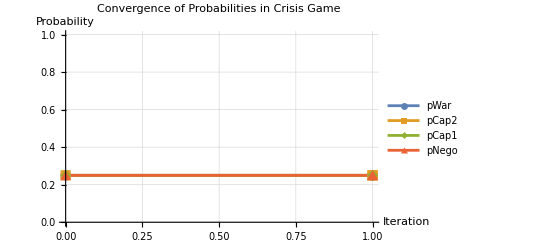

```mathematica
crisisConvergenceViz[[2]]
```

#### Full Game

```mathematica
fullResult=FindFullEquilibrium[sampleCase["U1War"],
							sampleCase["U1Cap1"],
							sampleCase["U1Cap2"],
							sampleCase["U1Nego"],
							sampleCase["U1SQ"],
							sampleCase["U1Acq1"],
							sampleCase["U1Acq2"],
							sampleCase["U2War"],
							sampleCase["U2Cap2"],
							sampleCase["U2Cap1"],
							sampleCase["U2Nego"],
							sampleCase["U2SQ"],
							sampleCase["U2Acq1"],
							sampleCase["U2Acq2"],
							lambda,
							dt1,
							dt2,
							dt3,
							dt4,
							maxIter,
							threshold,
							verboseMode];
```

```mathematica
(* visualise results *)
```

```mathematica
fullGameConvergenceViz = PlotDemandsConvergence[fullResult["DemandsIterationHistory"]];
CreateSummaryTable[fullResult]
```

```mathematica
fullGameConvergenceViz[[1]]
```

```mathematica
fullGameConvergenceViz[[2]]
```

#### Find Optimal Probabilities

```mathematica
optimalPhases=FindOptimalPhases[
preparedData[[1;;NumSamples]],(*Use subset for testing*)
lambda,(*Lambda*)
1000,(*phaseGridSize value for testing*)
"RandomSampling",(*Using random sampling instead of grid search*)
500                    (*Number of random samples to try*)
];
```

```mathematica
VisualizeOptimalPhasesResult[optimalPhases,preparedData]
```

```mathematica
testData=preparedData[[NumSamples+1;;NumSamples+101]];
```

```mathematica
VisualizePredictionAccuracy[optimalPhases,testData]
```